## Perturbation Analysis EP3

```mathematica
Clear["Global`*"]
```

```mathematica
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,1,1/2},{1,Δ+I γ,Ω/2},{1/2,Ω/2,0}}(*-1/2IdentityMatrix[3]*)];
EPHam0=ham[3/4,1,γ];
EPHam0//MatrixForm
```

(3/4-ⅈ γ | 1 | 1/2
1 | 3/4+ⅈ γ | 1/2
1/2 | 1/2 | 0)

```mathematica
γs=γ/.Solve[Discriminant[Det[EPHam0-e IdentityMatrix[3]],e]==0&&γ∈Reals,γ]
```

{0,0,-(3 √3)/4,-(3 √3)/4,(3 √3)/4,(3 √3)/4}

```mathematica
EPHam0=ham[3/4,1,γs[[5]]];
eep=Eigenvalues[EPHam0]
```

{1/2,1/2,1/2}

```mathematica
EPHam[x_]:=EPHam0+{{-I x,0,0},{0,I x,0},{0,0,0}};
EPHam[x]//MatrixForm
```

(3/4-(3 ⅈ √3)/4-ⅈ x | 1 | 1/2
1 | 3/4+(3 ⅈ √3)/4+ⅈ x | 1/2
1/2 | 1/2 | 0)

```mathematica
THam[x_,ω_]:=Evaluate[Det[EPHam[x]-ω IdentityMatrix[3]]]
Collect[THam[x,ω],x](*//N*)
```

1/8-(3 ω)/4-3/2 √3 x ω-x^2 ω+(3 ω^2)/2-ω^3

```mathematica
Collect[(THam[x,ω])/.{ω->eep[[2]]+c1 x^(1/3)+c2 x^(2/3)},x]
```

(-(3 √3)/4-c1^3) x+(-(3 √3 c1)/2-3 c1^2 c2) x^(4/3)+(-(3 √3 c2)/2-3 c1 c2^2) x^(5/3)+(-1/2-c2^3) x^2-c1 x^(7/3)-c2 x^(8/3)

```mathematica
cls={c1,c2}/.Solve[{(-(3 √3)/4-c1^3)==0&&(-(3 √3 c1)/2-3 c1^2 c2)==0},{c1,c2}]
```

{{-(√3)/2^(2/3),1/2^(1/3)},{((-1)^(1/3) √3)/2^(2/3),(-1)^(2/3)/2^(1/3)},{-((-1)^(2/3) √3)/2^(2/3),-(-1/2)^(1/3)}}

```mathematica
E1=eep[[2]]+cls[[1,1]] x^(1/3)+cls[[1,2]] x^(2/3);
E2=eep[[2]]+cls[[2,1]] x^(1/3)+cls[[2,2]] x^(2/3);
E3=eep[[2]]+cls[[3,1]] x^(1/3)+cls[[3,2]] x^(2/3);
```

```mathematica
fixep1[x_]:=Expand[Simplify[ComplexExpand[Re[E3]]-ComplexExpand[Re[E1]],x∈Reals&&x>0]]
fixep2[x_]:=Expand[Simplify[ComplexExpand[Re[E3]]-ComplexExpand[Re[E2]],x∈Reals&&x>0]]
fixep3[x_]:=Expand[Simplify[ComplexExpand[Re[E2]]-ComplexExpand[Re[E1]],x∈Reals&&x>0]]
fixep1[x]
fixep2[x]
fixep3[x]
```

(3 √3 x^(1/3))/(2 2^(2/3))-(3 x^(2/3))/(2 2^(1/3))

0

(3 √3 x^(1/3))/(2 2^(2/3))-(3 x^(2/3))/(2 2^(1/3))

```mathematica
2^(-5/3)3 Sqrt[3]
```

(3 √3)/(2 2^(2/3))

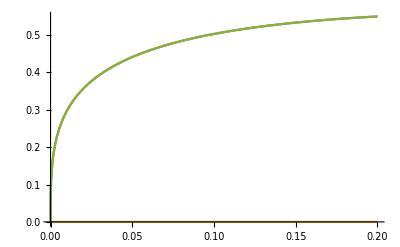

```mathematica
Plot[{fixep1[x],fixep2[x],fixep3[x]},{x,0,0.2}]
```

```mathematica
dat=Table[{γ-γs[[5]],ComplexExpand@Re[Eigenvalues[ham[3/4,1,γ]][[1]]]-ComplexExpand@Re[Eigenvalues[ham[3/4,1,γ]][[3]]]},{γ,N@γs[[5]],N@γs[[5]]+0.05,0.003}];
```

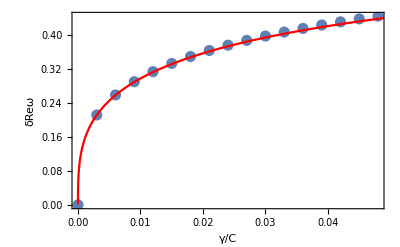

```mathematica
Show[ListPlot[dat,PlotStyle->{PointSize[0.02]}],Plot[fixep3[x],{x,0,0.05},PlotStyle->Red],Frame->True,FrameLabel->{"γ/C","δReω"}]
```

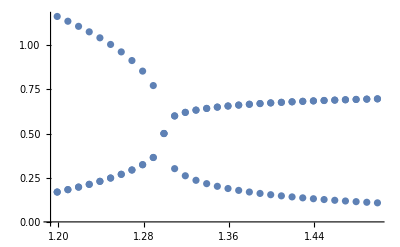

```mathematica
Show[ListPlot[Table[{γ,ComplexExpand@Re[Eigenvalues[ham[3/4,1,γ]][[1]]]},{γ,N@γs[[5]]-0.1,N@γs[[5]]+0.2,0.01}]],
ListPlot[Table[{γ,ComplexExpand@Re[Eigenvalues[ham[3/4,1,γ]][[2]]]},{γ,N@γs[[5]]-0.1,N@γs[[5]]+0.2,0.01}]],
ListPlot[Table[{γ,ComplexExpand@Re[Eigenvalues[ham[3/4,1,γ]][[3]]]},{γ,N@γs[[5]]-0.1,N@γs[[5]]+0.2,0.01}]]]
```

## Our Model Δ dependent

```mathematica
Clear["Global`*"]
```

```mathematica
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,1,Ω/2},{1,Δ+I γ,Ω/2},{Ω/2,Ω/2,0}}];
ham[Δ,Ω,γ]//MatrixForm
```

(-ⅈ γ+Δ | 1 | Ω/2
1 | ⅈ γ+Δ | Ω/2
Ω/2 | Ω/2 | 0)

```mathematica
Det[ham[9/10,3/5,γ]-e IdentityMatrix[3]]
```

9/500+(37 e)/100+(9 e^2)/5-e^3-e γ^2

```mathematica
Discriminant[Det[ham[9/10,3/5,γ]-e IdentityMatrix[3]],e]
```

(433-864300 γ^2+1920000 γ^4-1000000 γ^6)/250000

```mathematica
γs=γ/.Solve[Discriminant[Det[ham[9/10,3/5,γ]-e IdentityMatrix[3]],e]==0,γ];
γs//N
```

{-0.0223951,0.0223951,-0.848158,0.848158,-1.0955,1.0955}

```mathematica
ham[9/10,3/5,γs[[2]]]//Eigenvalues//N
```

{1.9902,-0.0951015,-0.0951015}

```mathematica
EPHam[λ_]:=ham[9/10,3/5,γs[[2]]]+{{λ,0,0},{0,λ,0},{0,0,0}};
EPHam[λ]//MatrixForm;
eep=Eigenvalues[EPHam[0]];
EPHam[λ]//N//MatrixForm
```

((0.9-0.0223951 ⅈ)+λ | 1. | 0.3
1. | (0.9+0.0223951 ⅈ)+λ | 0.3
0.3 | 0.3 | 0.)

```mathematica
f1[λ_]:=Evaluate[Chop[Simplify[ω/.NSolve[Det[EPHam[λ]-ω IdentityMatrix[3]]==0,ω]]][[1]]]
f2[λ_]:=Evaluate[Chop[Simplify[ω/.NSolve[Det[EPHam[λ]-ω IdentityMatrix[3]]==0,ω]]][[2]]]
f3[λ_]:=Evaluate[Chop[Simplify[ω/.NSolve[Det[EPHam[λ]-ω IdentityMatrix[3]]==0,ω]]][[3]]]
(*f4[λ_]:=Evaluate[Chop[Simplify[ω/.NSolve[Det[EPHam[λ]-ω IdentityMatrix[3]]==0,ω]]][[4]]]*)
```

```mathematica
FullSimplify[Evaluate[N@ComplexExpand[Re[f1[λ]]]-ComplexExpand[Re[f3[λ]]],λ∈Reals&&λ>0]]
```

$Aborted

```mathematica
Simplify[ComplexExpand[Re[f1[λ]]]-ComplexExpand[Re[f3[λ]]],λ∈Reals&&λ>0]
```

-((0.39685 (6.90281 Cos[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]]+2.85732 λ Cos[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]]+1.5874 λ^2 Cos[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]]+1. Cos[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]] ((-18.1359-11.511 λ+5.4 λ^2+2. λ^3+(λ^2 (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3)^2)^(1/4) Cos[0.5 Arg[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3]])^2+λ Abs[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3] Sin[0.5 Arg[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3]]^2)^(1/3)-3.98534 Sin[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]]-1.64968 λ Sin[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]]-0.916486 λ^2 Sin[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]]-0.57735 ((-18.1359-11.511 λ+5.4 λ^2+2. λ^3+(λ^2 (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3)^2)^(1/4) Cos[0.5 Arg[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3]])^2+λ Abs[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3] Sin[0.5 Arg[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3]]^2)^(1/3) Sin[1/3 Arg[-18.1359-11.511 λ+5.4 λ^2+2. λ^3+√(λ (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3))]]))/((-18.1359-11.511 λ+5.4 λ^2+2. λ^3+(λ^2 (9.07981-459.347 λ-408.045 λ^2-107.946 λ^3)^2)^(1/4) Cos[0.5 Arg[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3]])^2+λ Abs[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3] Sin[0.5 Arg[9.07981-459.347 λ-408.045 λ^2-107.946 λ^3]]^2)^(1/6))

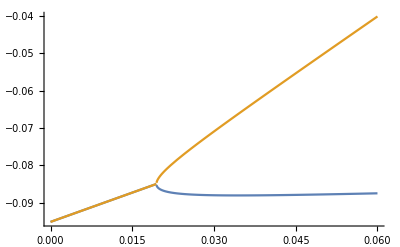

```mathematica
Plot[{ComplexExpand[Re[f1[λ]]],(*ComplexExpand[Re[f2[λ]]],*)ComplexExpand[Re[f3[λ]]]},{λ,0,0.06},PlotRange->All]
```

```mathematica
THam[λ_,ω_]:=Evaluate[Det[EPHam[λ]-ω IdentityMatrix[3]]]
```

```mathematica
Coe=Chop[Collect[THam[λ,ω]/.{ω->eep[[2]]+c1 λ^(1/3)+c2 λ^(2/3)+c3 λ^(3/3)},{λ}]];
Chop[Coe//N]
```

2.0853 c1^2 λ^(2/3)+(0.00927138-1. c1^3+4.17061 c1 c2) λ+(-2.18041 c1-3. c1^2 c2+2.0853 c2^2+4.17061 c1 c3) λ^(4/3)+(2. c1^2-2.18041 c2-3. c1 c2^2-3. c1^2 c3+4.17061 c2 c3) λ^(5/3)+(0.0951015+4. c1 c2-1. c2^3-2.18041 c3-6. c1 c2 c3+2.0853 c3^2) λ^2+(-1. c1+2. c2^2+4. c1 c3-3. c2^2 c3-3. c1 c3^2) λ^(7/3)+(-1. c2+4. c2 c3-3. c2 c3^2) λ^(8/3)+(-1. c3+2. c3^2-1. c3^3) λ^3

```mathematica
Simplify[Coefficient[Coe,λ]]
Simplify[Coefficient[Coe,λ^(4/3)]]
```

1/100 (-100 c1^3-60 c1 c2 (-6+Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459)+2 (-9-9 Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459+(Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459)^2)-c3 (-37-36 Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459+3 (Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459)^2+Root0.0502Root[-433+8643 #1-192 #1^2+#1^3&,1]0.050154210256008545))

1/10 (-30 c1^2 c2-3 c2^2 (-6+Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459)+c1 (-18-6 c3 (-6+Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459)+4 Root-0.951Root[{-433+864300 #1-1920000 #1^2+1000000 #1^3&,-18-37 #2+100 #1 #2-18 #2^2+#2^3&},{1,2}]-0.951015412387459))

```mathematica
cls={c1,c2}/.NSolve[{(Simplify[Coefficient[Coe,λ^(4/3)]])==0&&(Simplify[Coefficient[Coe,λ]])==0},{c1,c2}]
```

{{0.125992 (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(1/3),1/(19.3337-1.13687×10^-13 c3)(-143.984 (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)+276.112 c3 (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)-0.0793701 (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(5/3))},{(-0.0629961-0.109112 ⅈ) (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(1/3),1/(19.3337-1.13687×10^-13 c3)((71.9922-124.694 ⅈ) (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)-(138.056-239.12 ⅈ) c3 (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)+(0.039685-0.0687365 ⅈ) (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(5/3))},{(-0.0629961+0.109112 ⅈ) (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(1/3),1/(19.3337-1.13687×10^-13 c3)((71.9922+124.694 ⅈ) (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)-(138.056+239.12 ⅈ) c3 (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)+(0.039685+0.0687365 ⅈ) (-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(5/3))},{0.125992 (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(1/3),1/(19.3337-1.13687×10^-13 c3)(-143.984 (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)+276.112 c3 (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)-0.0793701 (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(5/3))},{(-0.0629961-0.109112 ⅈ) (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(1/3),1/(19.3337-1.13687×10^-13 c3)((71.9922-124.694 ⅈ) (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)-(138.056-239.12 ⅈ) c3 (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)+(0.039685-0.0687365 ⅈ) (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(5/3))},{(-0.0629961+0.109112 ⅈ) (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(1/3),1/(19.3337-1.13687×10^-13 c3)((71.9922+124.694 ⅈ) (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)-(138.056+239.12 ⅈ) c3 (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(2/3)+(0.039685+0.0687365 ⅈ) (-907.508+1739.4 c3+1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2))^(5/3))}}

```mathematica
E1=eep[[2]]+cls[[1,1]] x^(1/3)+cls[[1,2]] x^(2/3);
E2=eep[[2]]+cls[[2,1]] x^(1/3)+cls[[2,2]] x^(2/3);
```

```mathematica
fixep[x_]:=Expand[Simplify[ComplexExpand[Re[E2]]-ComplexExpand[Re[E1]],x∈Reals&&x>0]]
Simplify[fixep[x]]//N
```

-1/(19.3337-1.13687×10^-13 c3)414.168 (x^2 ((907.508-1739.4 c3+1.73205 ((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2)^(1/4) Cos[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]])^2+3. √((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2) Sin[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]]^2))^(1/6) (0.00882209 Cos[0.333333 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]]-5.18762×10^-17 c3 Cos[0.333333 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]]-0.000287456 x^(1/3) Cos[1.66667 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]] ((907.508-1739.4 c3+1.73205 ((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2)^(1/4) Cos[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]])^2+3. √((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2) Sin[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]]^2)^(2/3)-0.52147 Cos[0.666667 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]] (x^2 ((907.508-1739.4 c3+1.73205 ((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2)^(1/4) Cos[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]])^2+3. √((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2) Sin[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]]^2))^(1/6)+1. c3 Cos[0.666667 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]] (x^2 ((907.508-1739.4 c3+1.73205 ((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2)^(1/4) Cos[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]])^2+3. √((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2) Sin[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]]^2))^(1/6)-0.00509344 Sin[0.333333 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]]+2.99507×10^-17 c3 Sin[0.333333 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]]-0.301071 (x^2 ((907.508-1739.4 c3+1.73205 ((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2)^(1/4) Cos[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]])^2+3. √((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2) Sin[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]]^2))^(1/6) Sin[0.666667 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]]+0.57735 c3 (x^2 ((907.508-1739.4 c3+1.73205 ((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2)^(1/4) Cos[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]])^2+3. √((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2) Sin[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]]^2))^(1/6) Sin[0.666667 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]]-0.000165963 x^(1/3) ((907.508-1739.4 c3+1.73205 ((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2)^(1/4) Cos[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]])^2+3. √((274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)^2) Sin[0.5 Arg[274525.-1.05235×10^6 c3+1.0085×10^6 c3^2]]^2)^(2/3) Sin[1.66667 Arg[-907.508+1739.4 c3-1.73205 √(274525.-1.05235×10^6 c3+1.0085×10^6 c3^2)]])

```mathematica
dat=Table[{δ,ComplexExpand@Re[Eigenvalues[EPHam[δ]][[2]]]-ComplexExpand@Re[Eigenvalues[EPHam[δ]][[3]]]},{δ,0,0.05,0.003}];
```

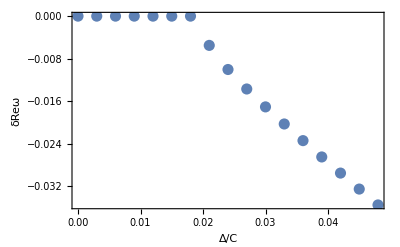

```mathematica
Show[ListPlot[dat,PlotStyle->{PointSize[0.02]}],Plot[fixep[x],{x,0,0.05},PlotStyle->Red],Frame->True,FrameLabel->{"Δ/C","δReω"}]
```

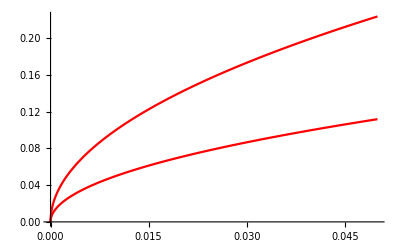

```mathematica
Show[Plot[x^(1/2),{x,0,0.05},PlotStyle->Red],Plot[.5 x^(1/2),{x,0,0.05},PlotStyle->Red]]
```

## 2Ls Δ dependent

```mathematica
Clear["Global`*"]
```

```mathematica
ham[Δ_,γ_]:=Evaluate[{{Δ-I γ,1},{1,Δ+I γ}}];
ham[1,1/Sqrt[2]]//MatrixForm
```

(1-ⅈ/(√2) | 1
1 | 1+ⅈ/(√2))

```mathematica
EPHam[λ_]:=ham[0,1]+{{λ,0},{0,0}};
EPHam[λ]//MatrixForm
eep=Eigenvalues[ham[0,1]]
```

(-ⅈ+λ | 1
1 | ⅈ)

{0,0}

```mathematica
THam[λ_,ω_]:=Evaluate[Det[EPHam[λ]-ω IdentityMatrix[2]]]
```

```mathematica
Collect[THam[λ,ω]/.{ω->eep[[2]]+c1 λ^(1/2)+c2 λ},λ]
```

(ⅈ+c1^2) λ+(-c1+2 c1 c2) λ^(3/2)+(-c2+c2^2) λ^2

```mathematica
cls={c1,c2}/.Solve[{(ⅈ+c1^2)==0&&(-c1+2 c1 c2)==0},{c1,c2}]
```

{{-(-1)^(3/4),1/2},{(-1)^(3/4),1/2}}

```mathematica
E1=eep[[2]]+cls[[1,1]] x^(1/2)+cls[[1,2]] x^(2/2);
E2=eep[[2]]+cls[[2,1]] x^(1/2)+cls[[2,2]] x^(2/2);
(*E3=eep[[2]]+cls[[3,1]] x^(1/3)+cls[[3,2]] x^(2/3);*)
```

```mathematica
fixep3[x_]:=Expand[Simplify[ComplexExpand[Re[E1]]-ComplexExpand[Re[E2]],x∈Reals&&x>0]]
fixep3[x]
```

√2 √x

```mathematica
dat=Table[{δ,ComplexExpand@Re[Eigenvalues[EPHam[δ]][[1]]]-ComplexExpand@Re[Eigenvalues[EPHam[δ]][[2]]]},{δ,0,0.05,0.003}]
```

{{0.,-3.82133×10^-16},{0.003,0.0774887},{0.006,0.109627},{0.009,0.134315},{0.012,0.155152},{0.015,0.17353},{0.018,0.190164},{0.021,0.205478},{0.024,0.219747},{0.027,0.233165},{0.03,0.245869},{0.033,0.257967},{0.036,0.269538},{0.039,0.28065},{0.042,0.291353},{0.045,0.301692},{0.048,0.311703}}

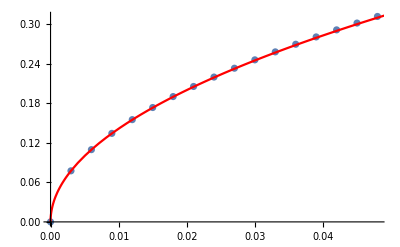

```mathematica
Show[ListPlot[dat],Plot[fixep3[x],{x,0,0.05},PlotStyle->Red]]
```